```mathematica
Quit
```

# Commuting, Migration, and Local Employment Elasticities

## by Ferdinando Monte, Stephen J. Redding and Esteban Rossi-Hansberg

American Economic Review, forthcoming 2018

This Mathematica notebook generates data for the counterfactual simulations with partially locally owned and partially nationally owned land and endogenous deficits.

The section “Setup, Import Data” sets up the simulation, loads external data, and computes portfolio (iota) shares.

The section “Functions” compiles routines to be used in the subsequent analysis.

The section “Data Preparation” computes productivities and county-level trade deficits.

The section “Counterfactual Simulations” performs the exercise in the web appendix.

## Setup, Import Data

## Initial data import and setup

### Setup

Setting history length to zero to avoid large memory usage during iterations

```mathematica
$HistoryLength=0;
SetDirectory["E:\\CMLEE"];
```

### Importing county data

This section imports data about initial equilibrium variables at county level.

```mathematica
(*Workplace data*)
workplaceEmp=Flatten[Import["simulation inputs\\workplaceEmp.csv"]]; (*number of jobs*)
workplaceWage=Flatten[Import["simulation inputs\\workplaceWage.csv"]];(*average yearly wage of a job by workplace, dollars*)
laborIncome=(workplaceEmp workplaceWage)/10^6; (*total payment to workers in a workplace, in millions*)

(*Residence data*)
resWage=Flatten[Import["simulation inputs\\residentialWage.csv"]];(*average yearly wage of a job by residence, dollars*)
resEmp=Flatten[Import["simulation inputs\\residentialEmp.csv"]];(*number of residents in a residential location*)
resIncome=Flatten[Import["simulation inputs\\resIncome.csv"]]; (*total residential income, millions*)

(*bilateral distances*)
distancesOnlyTrading=Import["simulation inputs\\distances_onlytrading.csv"]; (* when two counties do not trade, distance is 10^9; a row is an origin county, selling to all destination-columns counties (see below as well) *)
distancesAllPairs=Import["simulation inputs\\distances_allpairs.csv"]; (*distances when all counties are allowed to trade - all bilateral distances*)

(*commuters residing in a row location and working in a column location*)
λ=Import["simulation inputs\\commuting_flows.csv"];  

(*land area*)
landArea=Flatten[Import["simulation inputs\\land_area.csv"]];

(*other*)
countyNames=Import["simulation inputs\\county_names.csv"]; 
ncounties=Length[workplaceEmp];
```

### Importing other data

Correspondence between counties and cfs area. It is used in recovering the bilateral productivity estimates. 
The first column is a CFS identifier, the second is a county identifier (different from the fips code) from 1 to 3,111. Counties are always ordered by fips code, so the first row (or the first column) in the costMeasure and shares data is county number 1 in this data.

```mathematica
beaCfs=Import["simulation inputs\\bea_cfs_list.csv"];
Dimensions[beaCfs]
beaCfs[[1;;4]]
```

### Parameters

```mathematica
σ=4;
ψ=-1.2922/(1-σ);(*this ψ(1-σ) comes from the estimated gravity coefficient on CFS-level regressions*)
α=0.6;
ϵ=3.3035;
ϕ =4.4295/ϵ;
ηzero=Table[0,{i,1,ncounties}];
```

### Fixed variable values

These variables are used in the counterfactual exercises (compiled function and the iteration modules), and never change across simulations.

Matrix with indicators for whether a pair is a commuting possibility; the matrix with commuting flows (persons rather than shares) is λ:

```mathematica
isCommuting=Table[If[λ[[i,j]]==0,0,1],{i,1,ncounties},{j,1,ncounties}];
isCommutingSp=SparseArray[isCommuting];
isNoCommuting=DiagonalMatrix[Table[1,{i,1,ncounties}]];
isNoCommutingSp=SparseArray[isNoCommuting];
```

Total population (number of jobs)

```mathematica
population=Total[workplaceEmp];
```

## Assigning deficits and computing iota shares

This step occurs here so that we can compute the values of the shares iotas before the rest of the functions is compiled. The details of the calibration of this parameter are reported in Section B.17 of the web appendix.

### Importing CFS data

The n-th row in the beaCfs data (n=1 to 3111) has two elements: the CFS number F and the county number C. Here I generate a list of 123 elements; the k-th element contains the list of counties belonging to the k-th CFS area: the set of instructions in the “table” command below say: 1) “assign the county number C (in the second element) to the list number F (in the first element); 2) record in which position in this list the county C is placed (the first, the second.... in the corresponding CFS); this index is necessary to go back from the beaCfs correspondence to the beaCfs file.

```mathematica
beaCfsCorr=Table[{},{i,1,123}];
beaCfsIndex={};
Table[Block[{},
beaCfsCorr[[ beaCfs[[n,1]] ]]=Join[beaCfsCorr[[ beaCfs[[n,1]] ]],{beaCfs[[n,2]]}];
beaCfsIndex=Join[beaCfsIndex,{Length[beaCfsCorr[[ beaCfs[[n,1]] ]]]}];
],{n,1,ncounties}];
```

```mathematica
Total[Table[Length[beaCfsCorr[[i]]],{i,1,123}]]
```

Importing CFS trade data: sales from a CFS origin (row) to any CFS destination (column)

```mathematica
cfsData=Import["simulation inputs\\bilateral_cfs_trade.csv"];
Dimensions[cfsData]
```

Statistics on CFS deficits as a share of expenditure;

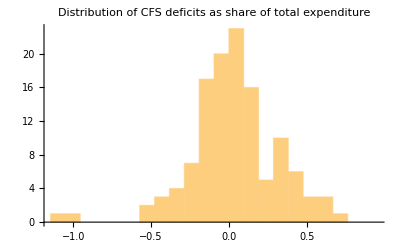

Mean: 0.033; Min: -1.145; Max: 0.952

quantile | CFS deficit
0.01 | -0.984
0.05 | -0.395
0.1 | -0.275
0.5 | 0.019
0.9 | 0.395
0.95 | 0.478
0.99 | 0.737

```mathematica
defExpenditure=(Total[cfsData]-Total[cfsData,{2}])/Total[cfsData];
Histogram[defExpenditure,{Min[defExpenditure],Quantile[defExpenditure,0.999],Quantile[defExpenditure,0.999]/10},
PlotLabel->"Distribution of CFS deficits as share of total expenditure"]
Print["Mean: ",Round[Mean[defExpenditure],0.001],"; Min: ",Round[Min[defExpenditure],0.001],"; Max: ",Round[Max[defExpenditure],0.001]];
Join[{{"quantile","CFS deficit"}},Table[{q,Quantile[Round[defExpenditure,0.001],q]},{q,{0.01,0.05,0.10,0.50,0.90,0.95,0.99}}]]//TableForm
```

### CFS trade deficits and allocation to counties

To allow for county level trade deficits, we compute the deficit at CFS level and then we impute this deficit at county-level in proportion to the residential income of each county. In general, it is not guaranteed that total expenditure is always positive for locations which are running a surplus. Hence, we rescale the CFS trade flows to match labor payments.

Creating a vector of labor payments to CFS workers (and checking they sum up to the total labor payment in the economy)

```mathematica
cfsLabExp=Table[{},{i,1,123}];
Table[cfsLabExp[[k]]=Table[laborIncome[[j]],{j,beaCfsCorr[[k]]}],{k,1,123}];
cfsLabExp=Total[cfsLabExp,{2}];
Total[cfsLabExp]-Total[laborIncome]
```

Creating a rescaled CFS trade matrix, where 1) total sales of any (row) origin match up to these cfs labor expenditure, keeping the destination composition of each origin fixed. The rationale is that total sales of a CFS, in a labor-only world, match to total labor payments to workers in the CFS (irrespective of their residence). We create a trade structure that matches the destination composition and the level of labor payments.

```mathematica
rescaledCfs=cfsData/Total[cfsData,{2}]  cfsLabExp;
```

The sum across rows of a given column gives a bea-consistent measure of expenditure of the CFS; hence, we can compute the cfs deficit as

```mathematica
cfsDeficit=Total[rescaledCfs]-Total[rescaledCfs,{2}];
```

This deficit is allocated across all counties that belong to the same CFS in proportion to their residential income. 
The table cfsResIncome contains for each CFS, a list of the residential incomes of all the counties; the table Increments contains, for each cfs k, a list of the addition to the residential income of all the counties in that cfs, as implied by the CFS deficit.

```mathematica
cfsResIncome=Table[{},{i,1,123}];
Table[cfsResIncome[[k]]=Table[resIncome[[j]],{j,beaCfsCorr[[k]]}],{k,1,123}];
increments=Table[cfsResIncome[[k]]/Total[cfsResIncome[[k]]] cfsDeficit[[k]],{k,1,123}];
resExpenditure=resIncome;
Table[resExpenditure[[i]]=resExpenditure[[i]]+ increments[[ beaCfs[[i,1]],beaCfsIndex[[i]] ]],{i,1,ncounties}];
resExpenditure=resExpenditure/α; (*this step is different in this calibration*)
```

Statistics on county-level deficits, as a share of county residential income

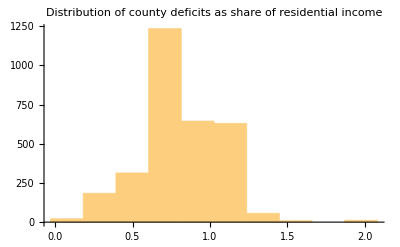

Mean: 0.821; Min: -0.03; Max: 12.499

quantile | county deficit
0.01 | 0.211
0.05 | 0.295
0.1 | 0.503
0.5 | 0.794
0.9 | 1.134
0.95 | 1.136
0.99 | 1.28

```mathematica
countyDeficit=resExpenditure/resIncome-1;

Histogram[countyDeficit,{Min[countyDeficit],Quantile[countyDeficit,0.999],Quantile[countyDeficit,0.999]/10},
PlotLabel->"Distribution of county deficits as share of residential income"]
Print["Mean: ",Round[Mean[countyDeficit],0.001],"; Min: ",Round[Min[countyDeficit],0.001],"; Max: ",Round[Max[countyDeficit],0.001]];
Join[{{"quantile","county deficit"}},Table[{q,Quantile[Round[countyDeficit,0.001],q]},{q,{0.01,0.05,0.10,0.50,0.90,0.95,0.99}}]]//TableForm
```

Comparing the distributions of deficits at cfs and county level

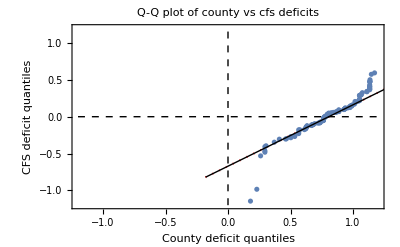

```mathematica
Show[
QuantilePlot[defExpenditure,countyDeficit,ReferenceLineStyle->Red,
FrameLabel->{"County deficit quantiles","CFS deficit quantiles"},PlotLabel->"Q-Q plot of county vs cfs deficits",PlotRange->{{-1.2,1.2},{-1.2,1.2}}],
ParametricPlot[{{0,x},{x,0}},{x,-1.2,1.2},PlotStyle->Directive[Black,Dashed,Thin]]]
```

Variable including the excess of expenditure over income

```mathematica
deficit=α resExpenditure-resIncome; (*in this calibration, the deficit is α resExpenditure - resIncome; in the file without end deficits, it is simply resExpenditure-resIncome*)
```

```mathematica
Min[resIncome+deficit]
```

0.646392

### Recovering iota shares

```mathematica
iota=Block[{lhs,mat1,mat2,mat3,mat3adj,mat4,rho,ρ,X,x,y,iota,ι,res,l},

lhs=α resExpenditure-resIncome;
lhs=Join[lhs[[1;;ncounties-1]],{1}];

rho=(1-α)resEmp/population;
mat1=Outer[Times,rho,resExpenditure];
mat2=(1-α)DiagonalMatrix[resExpenditure];
mat3=mat1-mat2;
mat3adj=Join[mat3[[1;;ncounties-1,1;;ncounties]],{Table[1,{i,1,ncounties}]}];
Print[DateString[]];
mat4=Inverse[mat3adj];
Print[DateString[]];
l=ncounties;
y=lhs[[1;;l]];
x=mat3[[1;;l,1;;l]];
iota=mat4.lhs;

iota
];
```

```mathematica
rentPC=((1-α)iota.resExpenditure)/population;
```

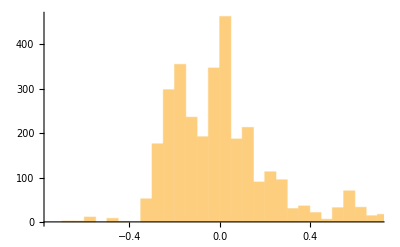

{-1.30181,-0.240835,0.276434,0.686948}

{-1.30181,1.15403}

```mathematica
Histogram[iota]
Quantile[iota,{0.0001,0.1,0.9,0.99}]
{Min[iota], Max[iota]}
```

## Functions

Productivity Estimates

Compiled function to compute new guess of labor income on a local labor market (this is the RHS of the iteration below, productivities)

```mathematica
rhsProductivities=Compile[{{prod,_Real,1},{num,_Real,2},{expenditure,_Real,1}},
Module[{bilatRes,multResistance,effDemand,leh},
bilatRes=num prod;(*proportional to bilateral cost*)
multResistance=Total[bilatRes]; (*denominator in RHS*)
effDemand=expenditure/multResistance; (*income/denominator in RHS*)
leh= bilatRes.effDemand; 
leh
](*RHS with current guess of productivity*)
];
```

Loop to compute productivities. This function receives 1) workplace employment (in persons), 2) workplace wage per person (in dollars), 3) total residential expenditure (in millions) and 4) a bilateral distance matrix (all pairs, or only county trading in the cfs data); residential expenditure allows for deficits.
It returns productivity levels that exactly rationalize the data on workplace income and residential expenditure. It uses the rhsProductivities function above to compute new rhs during the iterations.

```mathematica
productivities[workemp_,workwage_,resExp_,distmatrix_,detailsYN_]:=Module[{A0,λ,tol,c,dist,distmin,gap,labIncomeHat,A1,den,numerators,labIncome},
λ=0.7; (*step size *)
A0=Table[1.,{i,1,ncounties}]; (*initial condition for productivities*)

tol=10^-6; (*tolerance level*)
c=0;
dist=1;
numerators=(workemp (workwage/10^4)^(1-σ) ) (distmatrix)^(ψ(1-σ)); 
labIncome=(workemp workwage)/10^6; (*left hand side of trade flows equation*)

(*Note that the iterations solve for A^(σ-1); before returning the output, these guesses are rescaled to the 1/(σ-1).*)
While[dist>tol &&  c<10000,
c=c+1;

(*New labor Expenditure*)
labIncomeHat=rhsProductivities[A0,numerators,resExp];


 (*Relative gap in labor expenditure*)
gap=labIncome /labIncomeHat;
dist=Max[Abs[gap-1]];
distmin=Min[Abs[gap-1]];

 (*new guess of productivity*)
A1=(λ + (1-λ)gap)A0; 
den=Mean[A1];
A0=A1/den;

(*diagnostics*)
If[Mod[c,50]==1  && dist>0.01 && detailsYN==1,
Block[{},
Print["end of iteration ",c, " at " DateString[], "; min gap: ", distmin,"; max gap: ",dist,  " - ",Min[A0]," ",Max[A0]];
];
];
];
If[detailsYN==1,Block[{},
Print["end of iteration ",c, " at " DateString[], "; max gap: ",dist, " ",Min[A0]," ",Max[A0]];
]];
A0=A0^(1/(σ-1))/Mean[A0^(1/(σ-1))]; (*Recovering productivities from the A^(σ-1) values that fit the data*)
A0
];
```

Trade

Function to compute trade flows and trade shares given productivities, workplace employment and wage, residential expenditure, distance matrix.
The function returns 1) a matrix of trade shares - for each row origin, the shares of expenditure of each destination' s income on it, and 2) the corresponding trade flow values in millions of dollars.

```mathematica
trade=Compile[{{prod,_Real,1},{workemp,_Real,1},{workwage,_Real,1},{expenditure,_Real,1},{distmatrix,_Real,2}},
Module[{num,bilatRes,multResistance,share,trade},
num=(workemp (workwage/10^4)^(1-σ) ) (distmatrix)^(ψ(1-σ));
bilatRes=num prod^(σ-1);(*proportional to bilateral cost*)
multResistance=Total[bilatRes]; (*denominator in RHS*)
share=Transpose[Transpose[bilatRes]/multResistance ];
trade=Transpose[Transpose[share] expenditure];
{share,trade}
](*RHS with current guess of productivity*)
];
```

Counterfactual simulations

## Only changes in productivity

#### Guess Update

```mathematica
prodChangesGuess=Compile[{{inWhat,_Real,1},{inλ,_Real,2},{inXhat,_Real,1},{ahat,_Real,1},{ones,_Real,1},{χ,_Real,1}},

prodChangesGuessMod=Module[{iterVbar,iterLM,iterLR,iterQ,iterπni,iterP,iterRentPC,iterλtilde,iterWtilde,iterXtilde,distWages,distλ,wout,λout,diag,
temp1,temp2,temp3,temp4,temp5,temp6,denRes,numRes,den,num,den2,temp7,temp8,outcome},

(*vbar hat*)
denRes=λ.inWhat^ϵ;
numRes=λ.(inWhat^(ϵ+1) workplaceWage);
iterVbar=numRes/(resWage denRes);


(*lm hat and lr hat*)
(*note: λ are already flows, i.e. shares times Lbar in the equations*)
temp1=λ inλ;
iterLM=Total[temp1]/workplaceEmp;
iterLR=Total[Transpose[temp1]]/resEmp;


(*q hat*)

iterQ=(inXhat )^(1/(1+χ));

(*πni hat*)
temp2=iterLM (inWhat/ahat)^(1-σ);
den=temp2.πniOnlyTrading; (*note that left-product effectively gives the transpose of temp1 times temp2.*)
num=Outer[Times,temp2,ones];
iterπni=Transpose[Transpose[num]/den  ] ;(*the term inside divides each column by the correspondent element of the denominator; it then brings the matrix in the original form*)


(*P hat*)
diag=Table[iterπni[[i,i]],{i,1,ncounties}];
iterP=inWhat/ahat(iterLM/diag)^(1/(1-σ))  ;

(*rent per capita*)
iterRentPC=(iota.((1-α)resExpenditure inXhat))/(population rentPC);


(*w hat, next iteration*)
temp1=α πniOnlyTrading iterπni;

temp4=resExpenditure inXhat;
iterWtilde=(temp1.temp4)/(laborIncome iterLM);
iterWtilde=iterWtilde/Mean[iterWtilde];

(*Xhat, next iteration*)
iterXtilde=(resIncome iterVbar iterLR+rentPC resEmp iterRentPC iterLR+(1-α)(1-iota)resExpenditure inXhat)/resExpenditure;  


(*λ hat, next iteration*)
temp7=iterP^-α iterQ^(-1+α);
temp6=(Outer[Times,temp7,inWhat])^ϵ;
den2=Total[Total[λ temp6]];
iterλtilde=(temp6 population)/den2 ;  (*to limit accumulation of numerical errors - unconditional shares of commuting 
have a very small order of magnitude - we predict new commuting flows in # of jobs; hence, the numerator is multiplied by the population level before dividing it for the sum
of all terms at the denominator; note that the denominator contains λ, which is in fact flows of jobs, rather than shares*)

(*output*)
outcome=Join[iterλtilde,{iterWtilde},{iterXtilde}];
outcome

]
];
```

#### Iterations ( hatChangesA[ahat, landel, outputEvery] )

```mathematica
hatChangesA[ahat_,landel_,outputEvery_]:=Module[{dist,c,what,λhat,xhat,inWhat,inλ,inXhat,out,iterλtilde,iterWtilde,iterXtilde,distWages,distλ,distX,ones,
temp1,denRes,numRes,Vbarhat,LMhat,LRhat,Qhat,temp2,den,num,πnihat,diag,Phat,pricehat,realinchat,rentPChat},
dist=1;
c=0;
what=Table[1,{i,1,ncounties}];
xhat=Table[1,{i,1,ncounties}];
λhat=isCommuting;
ones=Table[1,{i,1,ncounties}];

While[c<maxiter && dist>tol,

c=c+1;
inWhat=what;
inXhat=xhat;
inλ=λhat;

out=prodChangesGuess[inWhat,inλ,inXhat,ahat,ones,landel];

iterλtilde=out[[1;;ncounties,All]] isCommutingSp;
iterWtilde=out[[ncounties+1,All]];
iterXtilde=out[[ncounties+2,All]];

distWages=Max[Abs[iterWtilde/inWhat-1]];
distX=Max[Abs[iterXtilde/inXhat-1]];

(*using the sparse-array version of commuting allows saving time*)
distλ=Max[Abs[iterλtilde/(inλ+isCommutingSp-1) -1] isCommutingSp];
(*the denominator makes sure that the division by zero never occurs, while preserving the deviations for observed commuting pairs; then, the matrix is multiplied by commuting indicators to restore zero change where there are no commuting flows*)
what=inWhat ζ + iterWtilde (1-ζ);
xhat=inXhat ζ+iterXtilde(1-ζ);
λhat=inλ  ζ + iterλtilde (1-ζ);

dist=Max[{distWages,distX,distλ}];

If[outputEvery>0 &&Mod[c,outputEvery]==1, Print["Iteration ",c,"  concluded on ",DateString[], "; distWages is ",distWages,"; distX is ",distX,"; distλ is ",distλ,"."]];
];
If[dist>tol,
Print["WARNING: Max iterations reached witout satisfying the required tolerance. Current sup-norm distances: distWages: ",distWages,"; distX is ",distX,"; distλ: ",distλ," ..."],
If[outputEvery>-1,
Print["Convergence achieved in ",c," iterations on ",DateString[],"; distWages is ",distWages,"; distX is ",distX,"; distλ is ",distλ," ..."]
]];

(*Computing equilibrium changes*)

(*vbar hat*)
denRes=λ.what^ϵ;
numRes=λ.(what^(ϵ+1) workplaceWage);
Vbarhat=numRes/(resWage denRes);


(*lm hat and lr hat*)
(*note: λ are already flows, i.e. shares times Lbar in the equations*)
temp1=λ λhat;
LMhat=Total[temp1]/workplaceEmp;
LRhat=Total[Transpose[temp1]]/resEmp;


(*q hat*)

Qhat=(xhat )^(1/(1+landel));  

(*πni hat*)
temp2=LMhat (what/ahat)^(1-σ);
den=temp2.πniOnlyTrading; (*note that left-product effectively gives the transpose of temp1 times temp2.*)
num=Outer[Times, temp2,ones];
πnihat=Transpose[Transpose[num]/den  ] ;(*the term inside divides each column by the correspondent element of the denominator; it then brings the matrix in the original form*)


(*P hat*)
diag=Table[πnihat[[i,i]],{i,1,ncounties}];
Phat=what/ahat(LMhat/diag)^(1/(1-σ))  ; 

(*price index hat*)
pricehat=Phat^α Qhat^(1-α);

(*real income of residents*)
realinchat=Vbarhat/pricehat; 

rentPChat=(iota.((1-α)resExpenditure xhat))/(population rentPC);




If[outputEvery>-1,Print["Counterfactuals completed on ",DateString[],"."]];


{what,Vbarhat,realinchat,LMhat,LRhat,Qhat,Phat,pricehat,λhat,πnihat,rentPChat,xhat,c,distWages,distλ,distX}

];
```

Other functions

## Productivity shocks to a set of counties

This function is used to simulate productivity shocks to one county (or a set of counties) inside a loop. It saves outcomes for all the economy with a given set of shocks, plus statistics on convergence used to check that all iterations concluded correctly.
It is used in 5% productivity shocks to counties and commuting zones, for example.

```mathematica
countyProdShock[rep_,prodChange_,landel_]:=Module[
{outcome,out,filename,caseN,repN,dataOutTreat,dataOutControl,measuredProdhat,shipmentsHat,allData,treatment,countyline,
whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,πnnhat,rentPChatOut,xhatOut,c,distWages,distλ,distX,replication,rentPChatTabOut},





(*computing outcome*)
outcome=hatChangesA[prodChange,landel,-1];

(*ALL COUNTIES OUTCOMES*)
	(*storing all counties outcome*)
	{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,rentPChatOut,xhatOut,c,distWages,distλ,distX}=outcome-1;
	
	{c,distWages,distλ,distX}={c,distWages,distλ,distX}+1;

	λhatOut=Diagonal[λhatOut]; (*own commuting change*)
	πnihatOut=Diagonal[πnihatOut];(*own trade share change*)
	measuredProdhat=((LMhatOut+1)/(πnihatOut+1))^(1/(σ-1))prodChange-1;(*measured productivity from cpi index*)
	shipmentsHat=(LMhatOut+1)(whatOut+1)-1;
	countyline=Table[i,{i,1,ncounties}];
	replication=Table[rep,{i,1,ncounties}];
	rentPChatTabOut=Table[rentPChatOut,{i,1,ncounties}];
	(*data to export*)
	allData={replication,countyline,whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,prodChange-1,measuredProdhat,shipmentsHat,rentPChatTabOut,xhatOut};

	Clear[out];
	out=Join[varnames,allData,2];
	out=Transpose[out];
	out=Join[countyNames,out,2];

	
	
Print[" Replication ", rep, " concluded at ",DateString[]];
(*the third column is 1 for treatment, 0 for control outcome*)
{out,c,distWages,distλ,distX}

];
```

## Data Preparation

Productivities and Associated Trade Flows

## Estimating productivities and county-level trade flows

Computing productivities given data

```mathematica
prodOnlyTrading=productivities[workplaceEmp,workplaceWage,α resExpenditure,distancesOnlyTrading,0];
```

Trade flows based on those productivities

```mathematica
{πniOnlyTrading,tradeOnlyTrading}=trade[prodOnlyTrading,workplaceEmp,workplaceWage,α resExpenditure,distancesOnlyTrading];
```

Testing trade shares sum to 1 by column and markets are clearing

```mathematica
{Min[Total[πniOnlyTrading]],Max[Total[πniOnlyTrading]]}
{Min[Total[tradeOnlyTrading]/(α resExpenditure)],Max[Total[tradeOnlyTrading]/(α resExpenditure)]}
```

## Counterfactual Simulations

a) 5% shock to one county at a time

Set up of the simulations:

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.6;
varnames={{"Repetition"},{"CountyLine"},{"WHat"},{"VbarHat"},{"RealIncHat"},{"LMhat"},{"LRhat"},{"QHat"},{"PHat"},{"PriceHat"},{"LambdaNNHat"},{"PiNNHat"},{"Ahat"},{"MeasuredProdHat"},{"ShipmentsHat"},{"RentPChat"},{"Xhat"}};
(*setting number of replications: one shock per county*)
numberOfReplications=3111;
(*complete matrix of shocks: row number N has the shock profile for repetition N*)
prodShocks=1+DiagonalMatrix[Table[0.05,{i,1,numberOfReplications}]];
```

Computing outcomes

```mathematica
out2=Parallelize[
Table[countyProdShock[rep,prodShocks[[rep]],ηzero],{rep,1,numberOfReplications}]
];
```

Exporting data in separate files

```mathematica
Print["Started on ",DateString[]];
Table[
Block[{repN,filename},
repN=ToString[rep];
If[rep<10,repN="000"<>repN];
If[rep≥10 && rep≤99,repN="00"<>repN];
If[rep≥100 && rep≤999,repN="0"<>repN];
filename="data\\county shocks 5pct endogDef\\county_oneShock5pct_rep"<>repN<>".csv";
Export[filename, out2[[rep,1]]];
],
{rep,1,numberOfReplications}];
Print["All export done on ",DateString[]];
```

Checking that all converged: max number of iteration is smaller than 2000, and distances from previous iteration smaller than 10^-6

```mathematica
{Max[Table[out2[[i,2]],{i,1,numberOfReplications}]],Max[Table[out2[[i,3]],{i,1,numberOfReplications}]],Max[Table[out2[[i,4]],{i,1,numberOfReplications}]]}
```